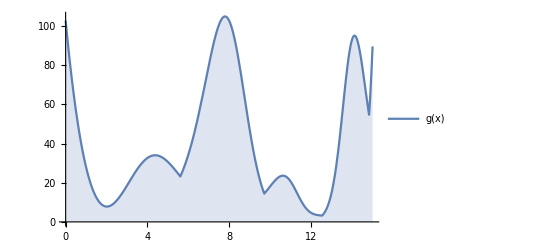

test.pdf

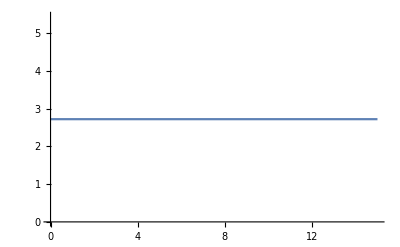

```mathematica
a:=Plot[(25+(x(x-6)(x-8)(x-14))/25)*E^Sqrt[1+Cos[x^2/10]],{x, 0, 15},Filling->Axis,PlotLegends->{"g(x)"}]
b:=ListLinePlot[{
{0,102.83},
{1,27.92}, 
{2,7.83},
{3,18.58},
{4,32.67},
{5,30.61},
{6,34.47},
{7,80.12},
{8,102.58},
{9,46.77},
{10,18.22},
{11,20.58},
{12,4.63},
{13,15.04},
{14,93.19},
{15,89.64}
}, PlotStyle->{Orange,Dashed},
Filling->Axis,
PlotLegends->{"f(x)"},
PlotMarkers->{Automatic, 10}]
a
Export["test.pdf",Show[a,b]]
```